```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Thu 1 Jun 2017

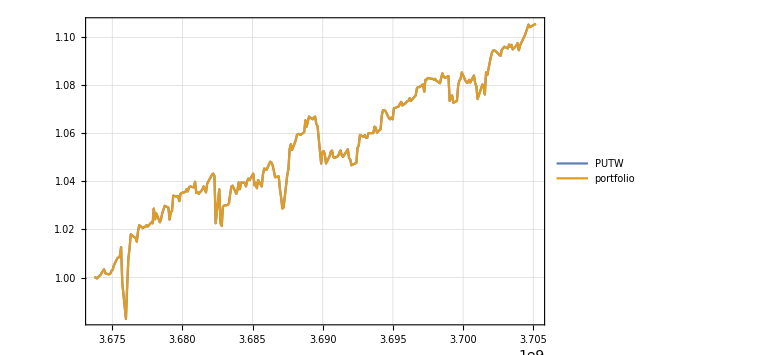
{-Graphics-,return | 1.10571
std | 0.0276131
r/s | 40.0428}

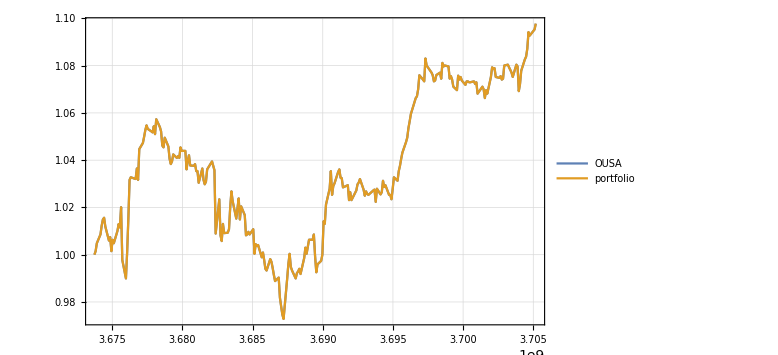
{-Graphics-,return | 1.09777
std | 0.0299607
r/s | 36.6403}

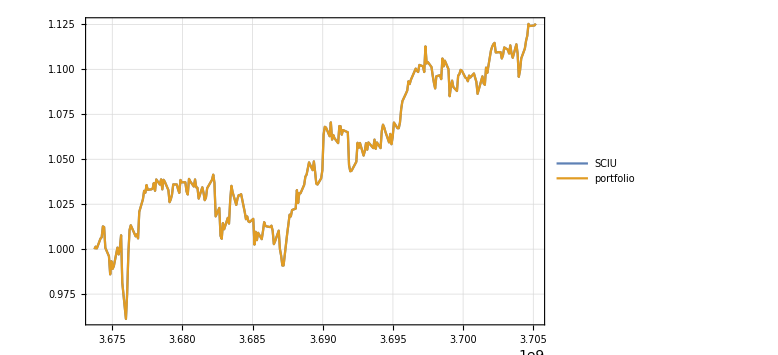
{-Graphics-,return | 1.1254
std | 0.0383773
r/s | 29.3245}

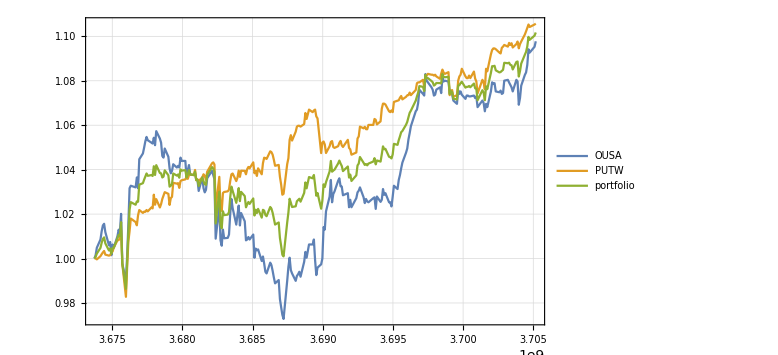
{-Graphics-,return | 1.10174
std | 0.0263054
r/s | 41.8825}

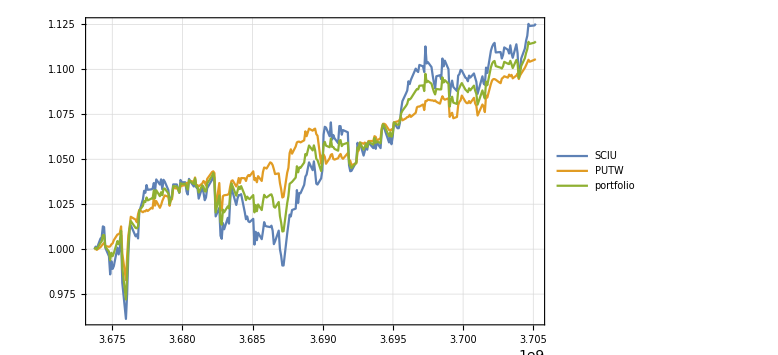
{-Graphics-,return | 1.11555
std | 0.0323393
r/s | 34.4953}

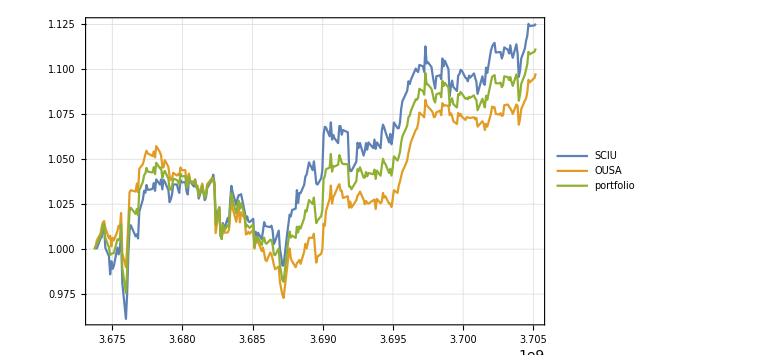
{-Graphics-,return | 1.11158
std | 0.033015
r/s | 33.669}

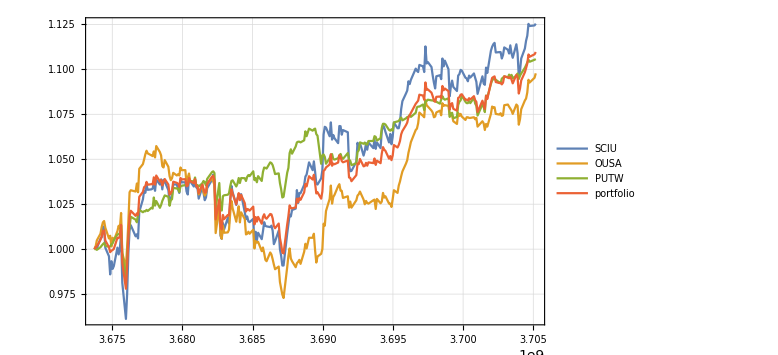
{-Graphics-,return | 1.10962
std | 0.0301445
r/s | 36.8101}

```mathematica
PortfolioChart[{"PUTW"},start1,end]
PortfolioChart[{"OUSA"},start1,end]
PortfolioChart[{"SCIU"},start1,end]
PortfolioChart[{"OUSA","PUTW"},start1,end]
PortfolioChart[{"SCIU","PUTW"},start1,end]
PortfolioChart[{"SCIU","OUSA"},start1,end]
PortfolioChart[{"SCIU","OUSA","PUTW"},start1,end]
```

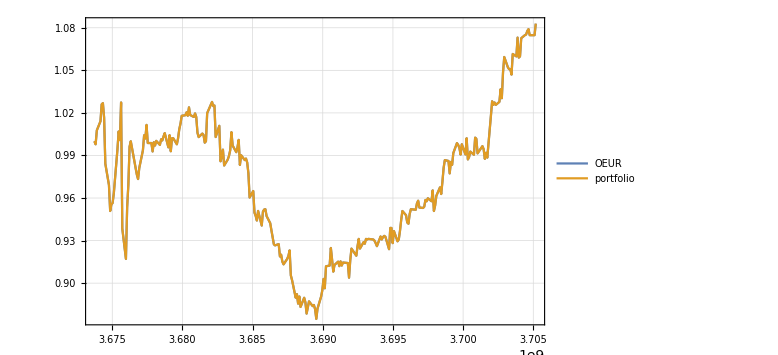
{-Graphics-,return | 1.08291
std | 0.047753
r/s | 22.6772}

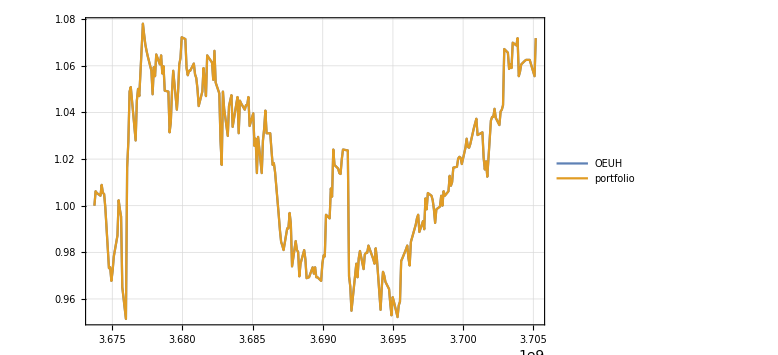
{-Graphics-,return | 1.07187
std | 0.0339981
r/s | 31.5274}

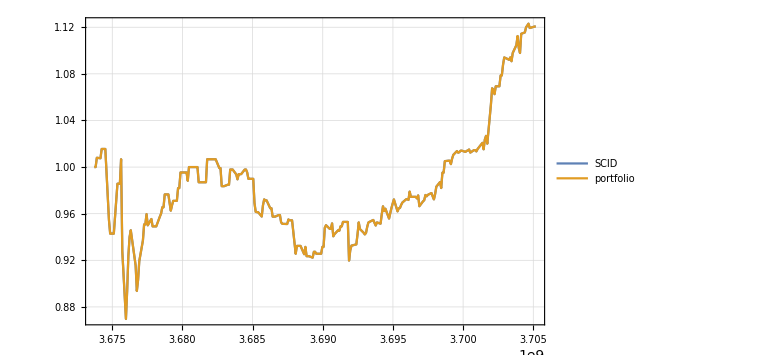
{-Graphics-,return | 1.12059
std | 0.0480814
r/s | 23.3061}

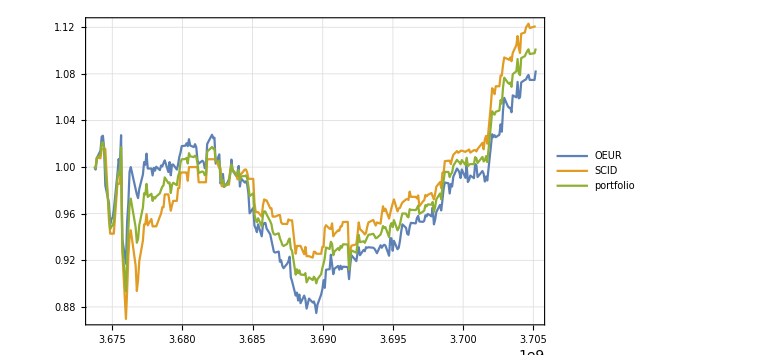
{-Graphics-,return | 1.10175
std | 0.0456846
r/s | 24.1164}

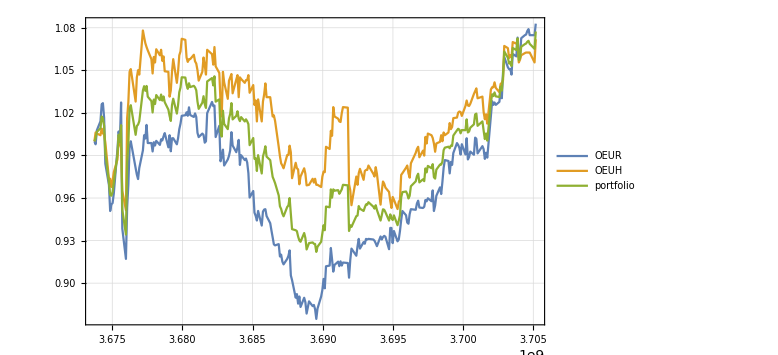
{-Graphics-,return | 1.07739
std | 0.0387099
r/s | 27.8324}

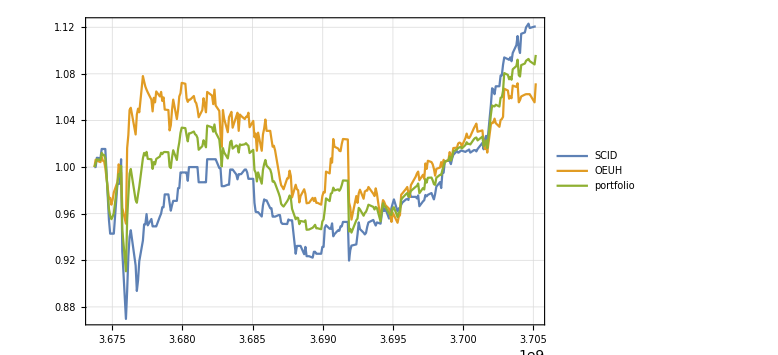
{-Graphics-,return | 1.09623
std | 0.0361465
r/s | 30.3274}

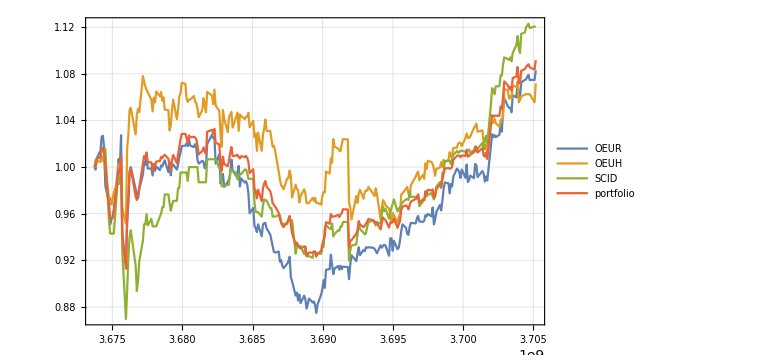
{-Graphics-,return | 1.09179
std | 0.0391867
r/s | 27.8612}

```mathematica
PortfolioChart[{"OEUR"},start1,end]
PortfolioChart[{"OEUH"},start1,end]
PortfolioChart[{"SCID"},start1,end]
PortfolioChart[{"OEUR","SCID"},start1,end]
PortfolioChart[{"OEUR","OEUH"},start1,end]
PortfolioChart[{"SCID","OEUH"},start1,end]
PortfolioChart[{"OEUR","OEUH","SCID"},start1,end]
```

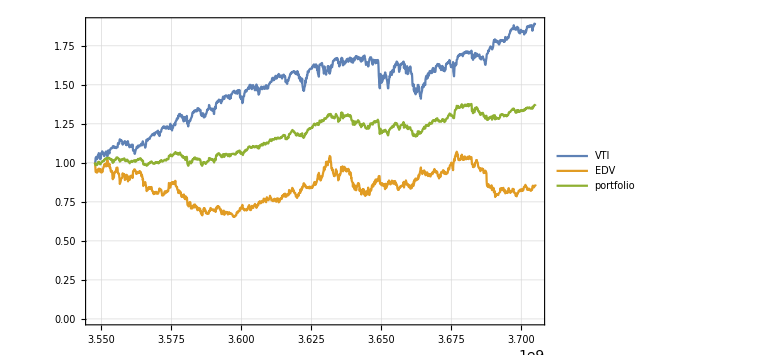
{-Graphics-,return | 1.37467
std | 0.123044
r/s | 11.1721}

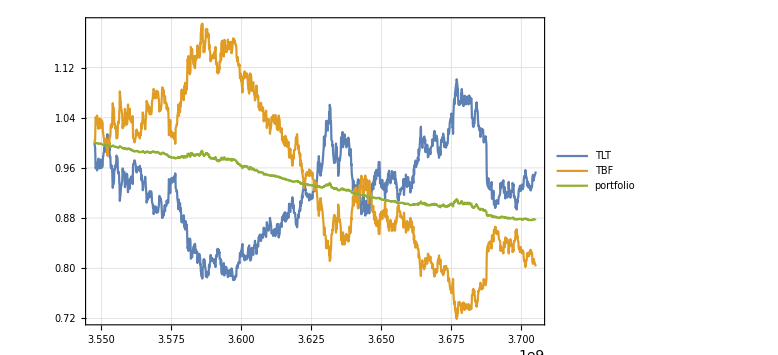
{-Graphics-,return | 0.878663
std | 0.0381607
r/s | 23.0253}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

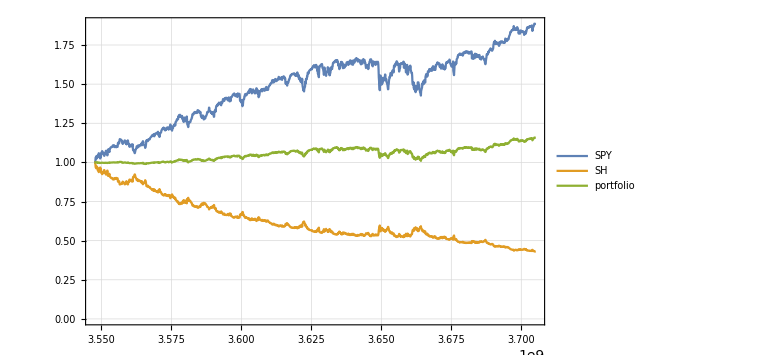
{-Graphics-,return | 1.1577
std | 0.0413499
r/s | 27.9976}

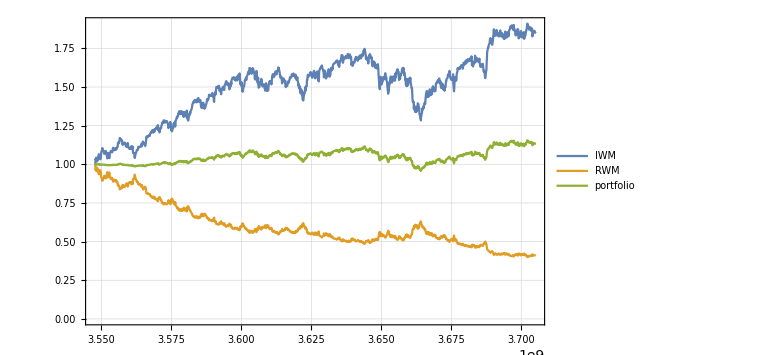
{-Graphics-,return | 1.13012
std | 0.0426497
r/s | 26.4978}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

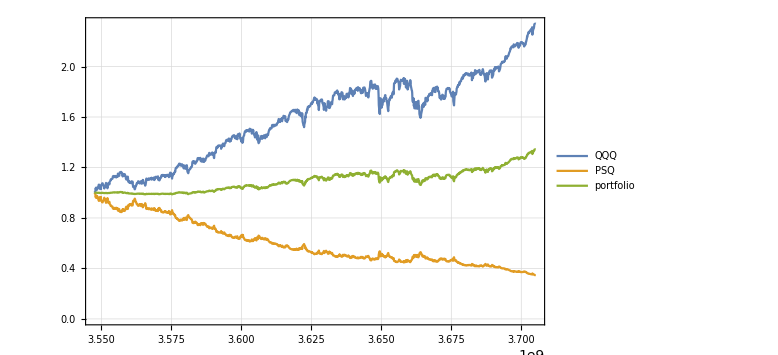
{-Graphics-,return | 1.34324
std | 0.0837298
r/s | 16.0425}

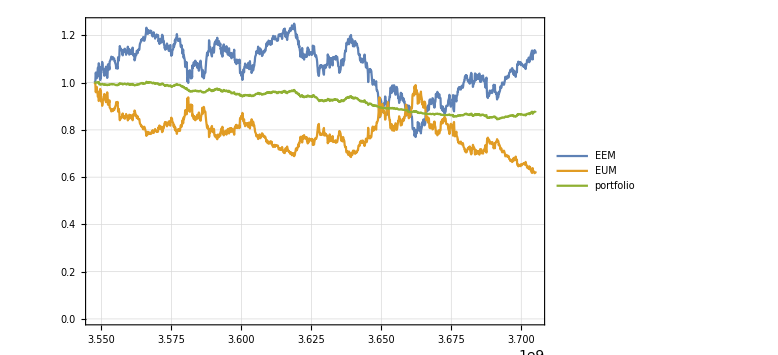
{-Graphics-,return | 0.873646
std | 0.0497301
r/s | 17.5677}

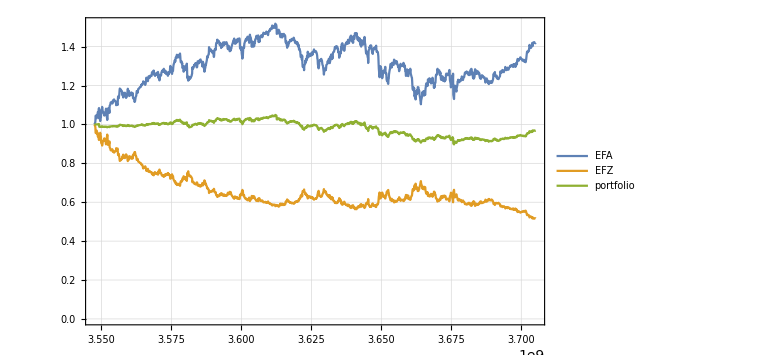
{-Graphics-,return | 0.96793
std | 0.0375715
r/s | 25.7623}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

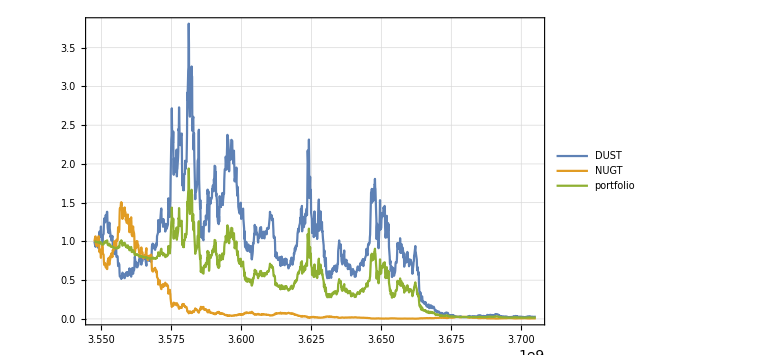
{-Graphics-,return | 0.0168998
std | 0.378091
r/s | 0.0446977}

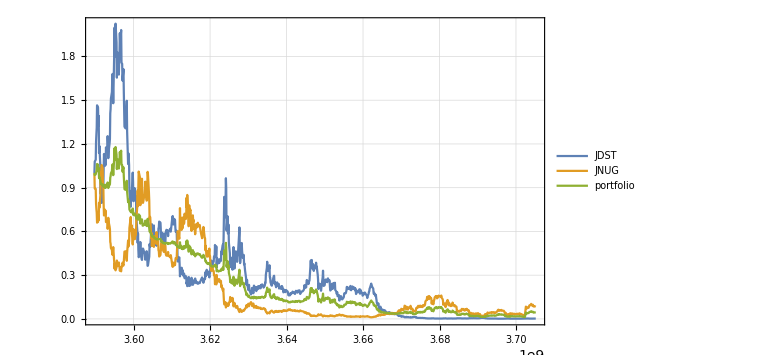
{-Graphics-,return | 0.0428643
std | 0.28604
r/s | 0.149854}

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```